## Manipulate Part 1

Hello and welcome. In this lecture, we will be looking at Manipulate Function.

### Introduction

Manipulate allows us to animate and look at functions over ranges of values. It essentially allows us to leverage the time dimension in visualizing data. In a previous lecture we saw that adding two Sine functions together that are out of phase from one another produces zero. Now let’s say that you wanted to understand how adding two Sine functions with differing phase values works. Let’s start with the following Manipulate:

```mathematica
Manipulate[ GraphicsRow[{
Plot[{Sin[x],Sin[x+phi]},{x,-2 Pi, 2 Pi},PlotRange->{Automatic,{-2,2}}],
Plot[Sin[x]+Sin[x+phi],{x,-2 Pi, 2Pi},PlotRange->{Automatic,{-2,2}}]
},ImageSize->Full],{phi,0,2 Pi}]
```

Here we have a slider that represents ϕ, which is the phase of one of our Sine functions. So what we are going to do is to add Sin[t] to Sin[t+ϕ]. Manipulate allows us to see how they change with respect to one another. In the graph on the left, we can see Sin[t+ϕ] moving to the left as we increase ϕ. And the right on the right, we see the amplitude changing, as well as its position. Manipulate can give us a good feel for how functions like these work.

### Visualizing Phase Offset

```mathematica
?Manipulate
```

Manipulate[expr,{u,u_min,u_max}] generates a version of expr with controls added to allow interactive manipulation of the value of u. 
Manipulate[expr,{u,u_min,u_max,du}] allows the value of u to vary between u_min and u_max in steps du. 
Manipulate[expr,{{u,u_init},u_min,u_max,…}] takes the initial value of u to be u_init. 
Manipulate[expr,{{u,u_init,u_lbl},…}] labels the controls for u with u_lbl. 
Manipulate[expr,{u,{u_1,u_2,…}}] allows u to take on discrete values u_1,u_2,…. 
Manipulate[expr,{u,…},{v,…},…] provides controls to manipulate each of the u,v,…. 
Manipulate[expr,c_u→{u,…},c_v→{v,…},…] links the controls to the specified controllers on an external device.

Manipulate basically takes an expression and the value you want to manipulate, a minimum value and a maximum value. So basically, it looks like the Plot function. It makes sense, because we are going to be manipulating and plotting, which essentially opens up two dimensions of freedom. So let’s begin by getting our Plot functions from before. So we are going to say:

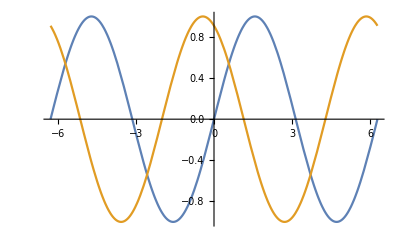

```mathematica
GraphicsRow[{
Plot[{Sin[x],Sin[x+2]},{x,-2 Pi, 2 Pi}]
}]
```

Our second function will be the sum of the two.

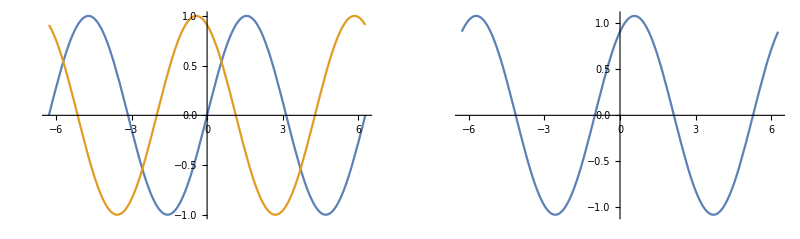

```mathematica
GraphicsRow[{
Plot[{Sin[x],Sin[x+2]},{x,-2 Pi, 2 Pi}],
Plot[Sin[x]+Sin[x+2],{x,-2 Pi, 2Pi}]
}]
```

Now we need to make this a little bigger. So we’ll say,

```mathematica
GraphicsRow[{
Plot[{Sin[x],Sin[x+2]},{x,-2 Pi, 2 Pi}],
Plot[Sin[x]+Sin[x+2],{x,-2 Pi, 2Pi}]
},ImageSize->Full]
```

-Graphics-

In our expression, we’re adding 2 to x in the Sin. This 2 represents the value that we want to manipulate – let’s turn it into a variable and then wrap it up in the Manipulate. Manipulate will be this entire expression of GraphicsRow. So let’s add the manipulate:

```mathematica
Manipulate[GraphicsRow[{
Plot[{Sin[x],Sin[x+phi]},{x,-2 Pi, 2 Pi}],
Plot[Sin[x]+Sin[x+phi],{x,-2 Pi, 2Pi}]
},ImageSize->Full],{phi,0,2 Pi}]
```

Test it out by dragging the ϕ slider. You’ll notice that the y-axis for right plot is changing scale under us. We need to make that axis stay between two values so that we can visually see the changing scale of the plot. We know that when we constructively add together, the maximum value is 2, and the minimum value is -2. So let’s use PlotRange to make our plots range from -2 to 2:

```mathematica
Manipulate[ GraphicsRow[{
Plot[{Sin[x],Sin[x+phi]},{x,-2 Pi, 2 Pi},PlotRange->{Automatic,{-2,2}}],
Plot[Sin[x]+Sin[x+phi],{x,-2 Pi, 2Pi},PlotRange->{Automatic,{-2,2}}]
},ImageSize->Full],{phi,0,2 Pi}]
```

Great! Now we have another tool at our disposal for visualizing data.

### Exploring Amplitude, Frequency and Phase Shift

Manipulate actually is a pretty rich function that allows you to explore many different characteristics of things. You have discrete things, you have continuous things. Here we saw a continuous value. What we are going to do now is to use Manipulate to build a mini app that will explore plots of various trigonometric functions, and it will allow us to change the amplitude, frequency and phase of those functions:

```mathematica
Manipulate[
Plot[A Sin[w t+phi],{t,-2Pi,2Pi},PlotRange->{Automatic,{-2,2}}],
{{A,0.5,"Amplitude"},0,2},
{{w,1,"Frequency"},0,10},
{{phi,0,"Phase Shift"},0,2Pi}]
```

Great, we now have three sliders labeled Amplitude, Frequency, and Phase shift. We can also make it so that we can choose between different trigonometric functions:

```mathematica
Manipulate[
Plot[A lambda[w t+phi],{t,-2Pi,2Pi},PlotRange->{Automatic,{-2,2}}],
{{A,0.5,"Amplitude"},0,2},
{{w,1,"Frequency"},0,10},
{{phi,0,"Phase Shift"},0,2Pi},
{{lambda,Sin,"Function"},{Sin,Cos,Tan,Cot}}]
```

Notice that Mathematica automatically noticed that the set of parameters to the functions part of Manipulate was discrete and it turned them into buttons.

### Summary

In this lecture we saw how to use Manipulate to create sliders and buttons, and to explore these functions, and explore the variables that parameterize them. We’ll be back in the next lecture with another video on Manipulate where we take a look at something a little bit more complicated, putting together some of the stuff we saw in graphics. Thanks and see you at the next lecture!